```mathematica
δ = 0.074;
w = 1.013;
```

```mathematica
0.074
```

0.074

```mathematica
0.074
```

0.074

```mathematica
0.074
```

0.074

```mathematica
sol = DSolve[{x''[t] + 2δ x'[t] + w^2 x[t] ==0, x[0] == 12, x'[0] == 18}, x[t], {t,0,50}];

sol2 = DSolve[{x2''[t] + 2 δ x2'[t] + w^2 x2[t]== 0, x2[0] == 0, x2'[0] == 6}, x2[t], {t, 0, 150}];
```

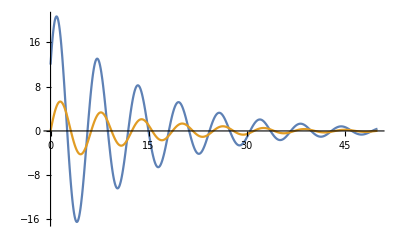

```mathematica
Plot[{x[t] /.sol, x2[t] /.sol2}, {t, 0, 50}, PlotRange -> All]
```

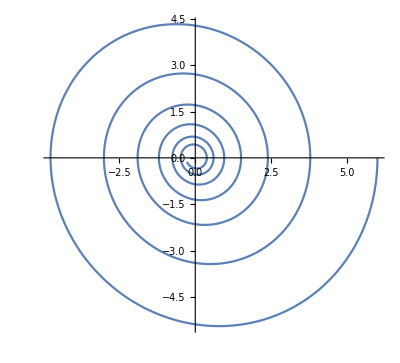

```mathematica
δ = 0.074;
w = 1.013;

sol = NDSolve[{x''[t] + 2δ x'[t] + w^2 x[t] ==0, x[0] == 6, x'[0] == 0},{x[t], x'[t]}, {t,0,40}];
ParametricPlot[Evaluate[{x[t], x'[t]}/.sol], {t, 0, 40}]
```